```mathematica
excitationsPDG={
N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,
D1232,D1600,D1620,D1700,D1905,D1910,D1920,D1950
};
excitationsUrQMD={
N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1900,N1990,N2080,N2190,N2220,N2250,
D1232,D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950
};
(* Matrix elements and cross-sections *)
ClearAll[matrixElement];ClearAll[meA];
matrixElement[eCM_,{N938,D1232}]:=40000 * (m0[D1232] Γ0[D1232])^2/((eCM^2 -m0[D1232]^2)^2 +( m0[D1232] Γ0[D1232])^2);
matrixElement[eCM_,{D1232,D1232}]:=2.8;
meA[N938,h_]:=If[MemberQ[Ns,h],3.6,12.0];
meA[D1232,h_]:=3.5;
matrixElement[eCM_,{hA_,hB_}]:=meA[hA,hB]/((m0@hA-m0@hB)^2(m0@hA+m0@hB)^2);

ClearAll[σDiffractiveNN];
σDiffractiveNN[eCM_,{hC_,hD_}]:=If[eCM≤2m0[N938],0,
(2j[hC]+1)(2j[hD]+1) * pMean[eCM,{hC,hD},1]/pMean[eCM,{N938,N938},1]* 1/eCM^2 * matrixElement[eCM,{hC,hD}]
];
σDiffractiveNN[eCM_]:=
Sum[σDiffractiveNN[eCM,{N938,h}]+σDiffractiveNN[eCM,{D1232,h}],{h,excitations}];

σDiffNN[n_,excitations_][eCM_]:=
Sum[σDiffractiveNN[eCM,{n,h}],{h,excitations}];

σDiffNNtoNNstar=σDiffNN[N938,{N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1900,N1990,N2080,N2190,N2220,N2250}];
σDiffNNtoND=σDiffNN[N938,{D1232}];
σDiffNNtoNDstar=σDiffNN[N938,{D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950}];
σDiffNNtoDNstar=σDiffNN[D1232,{N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1900,N1990,N2080,N2190,N2220,N2250}];
σDiffNNtoDD=σDiffNN[D1232,{D1232}];
σDiffNNtoDDstar=σDiffNN[D1232,{D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950}];
```

```mathematica
Monitor[σDiffNNtoDDstar[8.],h]//AbsoluteTiming
```

$Aborted

```mathematica
Monitor[σDiffNNtoDDstar[3.5],h]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{3.43296,2.95105}

```mathematica
Monitor[σDiffNNtoDDstar[8.],h]//AbsoluteTiming
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.61537 and 0.0107324 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 4.28465 and 0.0167603 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.67294 and 0.0102561 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

{114.581,2.24218}

```mathematica
WP=12:{612.832396,3.6890237173094924}
```

```mathematica
WP=2:{236.602202,3.2206849964510003}
```

{329.557,2.54569}

{554.309,3.39714}

{504.58,3.39715}

{165.39,3.64618}

```mathematica
a[D1620,3.5]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.851929}. NIntegrate obtained 1.4153 and 0.00764298 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.650555}. NIntegrate obtained 0.0555651 and 0.00011639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.851929}. NIntegrate obtained 0.966388 and 0.00566323 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.0574585

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.350073}. NIntegrate obtained 0.0000326406 and 3.5413×10^-8 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.650555}. NIntegrate obtained 0.0555651 and 0.00011639 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mB near {mB} = {0.650555}. NIntegrate obtained 0.257964 and 0.000418283 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

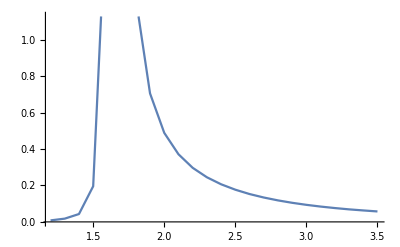
{1.79114,-Graphics-}

```mathematica
ListLinePlot[Table[{m,a[D1620,m]},{m,1.2,3.5,.1}]]//AbsoluteTiming
```

```mathematica
ptsDD=Table[{m,σDiffractiveNN[m,{D1232,D1232}]},{m,2.4,8.,.2}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{{2.4,0.0965412},{2.6,1.21037},{2.8,1.96451},{3.,2.31555},{3.2,2.45362},{3.4,2.47267},{3.6,2.42797},{3.8,2.34969},{4.,2.25299},{4.2,2.1478},{4.4,2.04067},{4.6,1.93502},{4.8,1.83262},{5.,1.7333},{5.2,1.64253},{5.4,1.55547},{5.6,1.4736},{5.8,1.39709},{6.,1.32557},{6.2,1.25876},{6.4,1.19631},{6.6,1.13803},{6.8,1.08342},{7.,1.03234},{7.2,0.984664},{7.4,0.939957},{7.6,0.898215},{7.8,0.858997},{8.,0.822231}}

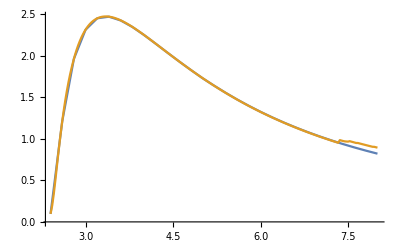

```mathematica
ListLinePlot[{ptsDD,urqmdppDD}]
```

```mathematica
AbsoluteTiming[
σDiffNNtoDNstar[4.]
]
```

$Aborted

```mathematica
σDiffractiveNN[4.,{D1232,N1675}]//AbsoluteTiming
```

{0.11617,1.99243}

```mathematica
σDiffractiveNN[3.5,{D1232,D1232}]
```

2.4566

```mathematica
pMean[3.5,{D1232,D1232},1]
```

0.992395

```mathematica
pCMS[3.5,1.7,1.79]
```

```mathematica
detbalin2[eCM_,mD_]:=NIntegrate[a[D1232,mD]pCMS[eCM,mC,mD]a[D1232,mC],{mC,minMass@D1232+0.0001,eCM-mD-0.0001}];
```

```mathematica
Block[{eCM=3.5},
NIntegrate[a[D1232,mD]pCMS[eCM,mC,mD]a[D1232,mC],{mD,1.077,1.232},{mC,minMass@D1232+0.0001,eCM-mD-0.0001}]
]
```

0.3651

```mathematica
pMean[3.5,{D1232,D1232},1]
```

0.992395

```mathematica
Block[{eCM=3.5},
NIntegrate[a[D1232,mD]pCMS[eCM,mC,mD]a[D1232,mC],{mD,minMass@D1232,eCM-minMass@D1232},{mC,minMass@D1232+0.0001,eCM-mD-0.0001}]
]
```

0.992389

```mathematica
detbalin2[3.5,1.7]
```

0.254269

```mathematica
Block[{eCM=3.5},
NIntegrate[ a[D1232,mD]pCMS[eCM,mC,mD] a[D1232,mC],{mD,minMass@D1232,eCM-minMass@D1232},{mC,minMass@D1232,eCM-mD}
]
]
```

0.99239

```mathematica
urqmdPts={
{1.200,5.5374},{1.212,6.5369},{1.223,6.6544},{1.234,6.0486},{1.246,5.1717},{1.257,4.3270},{1.269,3.6192},{1.280,3.0548},{1.292,2.6104},{1.303,2.2590},{1.315,1.9781},{1.327,1.7507},{1.338,1.5641},{1.349,1.4090},{1.361,1.2784},{1.373,1.1673},{1.384,1.0718},{1.395,0.9889},{1.407,0.9164},{1.418,0.8525},{1.430,0.7958},{1.442,0.7451},{1.453,0.6995},{1.464,0.6584},{1.476,0.6211},{1.487,0.5870},{1.499,0.5559},{1.510,0.5272},{1.522,0.5008},{1.533,0.4764},{1.545,0.4537},{1.556,0.4326},{1.568,0.4129},{1.579,0.3944},{1.591,0.3772},{1.603,0.3609},{1.614,0.3456},{1.625,0.3312},{1.637,0.3176},{1.648,0.3047},{1.660,0.2924},{1.671,0.2808},{1.683,0.2697},{1.694,0.2592},{1.706,0.2491},{1.717,0.2395},{1.729,0.2303},{1.740,0.2215},{1.752,0.2131},{1.764,0.2050},{1.775,0.1972},{1.786,0.1897},{1.798,0.1826},{1.809,0.1756},{1.821,0.1688},{1.833,0.1624},{1.844,0.1562},{1.855,0.1502},{1.867,0.1444},{1.878,0.1387},{1.890,0.1333},{1.901,0.1280},{1.913,0.1229},{1.924,0.1179},{1.936,0.1130},{1.947,0.1083},{1.959,0.1037},{1.970,0.0993},{1.982,0.0949},{1.993,0.0907},{2.005,0.0865},{2.016,0.0825},{2.028,0.0785},{2.039,0.0746},{2.051,0.0708},{2.062,0.0671},{2.074,0.0634},{2.085,0.0599},{2.097,0.0563},{2.108,0.0529},{2.120,0.0494},{2.131,0.0461},{2.143,0.0427},{2.154,0.0395},{2.166,0.0362},{2.177,0.0330},{2.189,0.0298},{2.200,0.0266},{2.212,0.0235},{2.223,0.0203},{2.235,0.0173},{2.247,0.0142},{2.258,0.0113},{2.269,0.0085},{2.281,0.0061},{2.292,0.0041},{2.304,0.0026}};
```

```mathematica
myPts=Table[
{mD,
a[D1232,mD]NIntegrate[pCMS[3.5,mC,mD]a[D1232,mC],{mC,minMass@D1232+0.0001,2.304}]
},{mD,1.2,3.5,2.3/200}];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mC near {mC} = {2.08334}. NIntegrate obtained 0.999561 and 1.11045×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mC near {mC} = {2.01379}. NIntegrate obtained 0.948882 and 1.251×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in mC near {mC} = {1.95624}. NIntegrate obtained 0.904473 and 1.1998×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
myPts
```

{{1.2,5.5369},{1.2115,6.53631},{1.223,6.65379},{1.2345,6.04799},{1.246,5.17122},{1.2575,4.32655},{1.269,3.61881},{1.2805,3.05457},{1.292,2.61015},{1.3035,2.25876},{1.315,1.97794},{1.3265,1.75057},{1.338,1.56397},{1.3495,1.40884},{1.361,1.27829},{1.3725,1.1672},{1.384,1.0717},{1.3955,0.988843},{1.407,0.91635},{1.4185,0.852439},{1.43,0.795707},{1.4415,0.745019},{1.453,0.699477},{1.4645,0.658341},{1.476,0.621003},{1.4875,0.586961},{1.499,0.555796},{1.5105,0.527163},{1.522,0.500745},{1.5335,0.476308},{1.545,0.453629},{1.5565,0.432522},{1.568,0.412826},{1.5795,0.394399},{1.591,0.377122},{1.6025,0.360886},{1.614,0.345597},{1.6255,0.331171},{1.637,0.317536},{1.6485,0.304624},{1.66,0.292379},{1.6715,0.280761},{1.683,0.26968},{1.6945,0.259138},{1.706,0.249081},{1.7175,0.239474},{1.729,0.230287},{1.7405,0.221491},{1.752,0.213059},{1.7635,0.204968},{1.775,0.197197},{1.7865,0.189724},{1.798,0.182531},{1.8095,0.175602},{1.821,0.168922},{1.8325,0.162474},{1.844,0.156247},{1.8555,0.150227},{1.867,0.144403},{1.8785,0.138764},{1.89,0.1333},{1.9015,0.128002},{1.913,0.122861},{1.9245,0.117868},{1.936,0.113016},{1.9475,0.108296},{1.959,0.103704},{1.9705,0.0992305},{1.982,0.0948703},{1.9935,0.0906174},{2.005,0.0864663},{2.0165,0.082411},{2.028,0.0784466},{2.0395,0.0745677},{2.051,0.0707692},{2.0625,0.0670469},{2.074,0.0633952},{2.0855,0.0598099},{2.097,0.0562863},{2.1085,0.0528198},{2.12,0.0494058},{2.1315,0.0460397},{2.143,0.0427168},{2.1545,0.0394327},{2.166,0.0361834},{2.1775,0.0329635},{2.189,0.0297705},{2.2005,0.0266008},{2.212,0.023453},{2.2235,0.020332},{2.235,0.0172442},{2.2465,0.0142149},{2.258,0.0112866},{2.2695,0.00852223},{2.281,0.00609512},{2.2925,0.00408745},{2.304,0.00259118},{2.3155,0.00157205},{2.327,0.00092098},{2.3385,0.000520522},{2.35,0.000281628},{2.3615,0.000143142},{2.373,0.0000663106},{2.3845,0.0000265151},{2.396,8.19552×10^-6},{2.4075,1.46588×10^-6},{2.419,3.58646×10^-8},{2.4305,0.},{2.442,0.},{2.4535,0.},{2.465,0.},{2.4765,0.},{2.488,0.},{2.4995,0.},{2.511,0.},{2.5225,0.},{2.534,0.},{2.5455,0.},{2.557,0.},{2.5685,0.},{2.58,0.},{2.5915,0.},{2.603,0.},{2.6145,0.},{2.626,0.},{2.6375,0.},{2.649,0.},{2.6605,0.},{2.672,0.},{2.6835,0.},{2.695,0.},{2.7065,0.},{2.718,0.},{2.7295,0.},{2.741,0.},{2.7525,0.},{2.764,0.},{2.7755,0.},{2.787,0.},{2.7985,0.},{2.81,0.},{2.8215,0.},{2.833,0.},{2.8445,0.},{2.856,0.},{2.8675,0.},{2.879,0.},{2.8905,0.},{2.902,0.},{2.9135,0.},{2.925,0.},{2.9365,0.},{2.948,0.},{2.9595,0.},{2.971,0.},{2.9825,0.},{2.994,0.},{3.0055,0.},{3.017,0.},{3.0285,0.},{3.04,0.},{3.0515,0.},{3.063,0.},{3.0745,0.},{3.086,0.},{3.0975,0.},{3.109,0.},{3.1205,0.},{3.132,0.},{3.1435,0.},{3.155,0.},{3.1665,0.},{3.178,0.},{3.1895,0.},{3.201,0.},{3.2125,0.},{3.224,0.},{3.2355,0.},{3.247,0.},{3.2585,0.},{3.27,0.},{3.2815,0.},{3.293,0.},{3.3045,0.},{3.316,0.},{3.3275,0.},{3.339,0.},{3.3505,0.},{3.362,0.},{3.3735,0.},{3.385,0.},{3.3965,0.},{3.408,0.},{3.4195,0.},{3.431,0.},{3.4425,0.},{3.454,0.},{3.4655,0.},{3.477,0.},{3.4885,0.},{3.5,0.}}

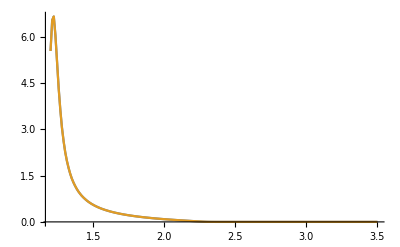

```mathematica
ListLinePlot[{myPts,urqmdPts},PlotRange->All]
```

```mathematica
{minMass@D1232,3.5-minMass@D1232}
```

{1.076,2.424}

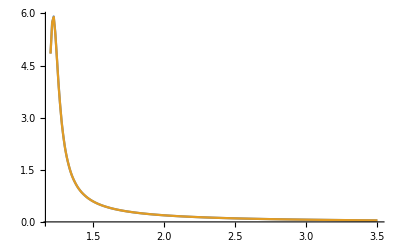

```mathematica
ListLinePlot[{myA,urqmdA},PlotRange->All]
```

```mathematica
minMass@D1232
```

1.076

```mathematica
3.5-2minMass@D1232
```

1.348

```mathematica
{mD,minMass@D1232,eCM-minMass@D1232}
```

{mD,1.076,-1.076+eCM}

```mathematica
detbalin2[3.5,1.8]
```

0.176725

```mathematica
minMass@D1232
```

1.076

```mathematica
Γ[D1232,3.5]
```

1.57023

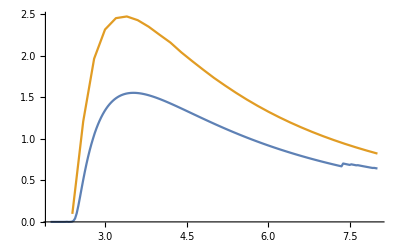

```mathematica
ListLinePlot[{urqmdppDD, ptsDD}]
```

```mathematica
minMass@N938+minMass@N1440
```

2.014

```mathematica
σDiffractiveNN[2.1,{N938,N1440}]
```

0.000807774

```mathematica
ListLinePlot[{urqmdppND,urqmdppDD,urqmdppNNstar,ptsND,ptsDD,ptsNNstar},PlotStyle->{Thick,Thick,Thick,Dashed,Dashed,Dashed},PlotRange->All]
```

-Graphics-

```mathematica
ptsND=Monitor[
Table[{m,σDiffNNtoND[m]},{m,2.,8.,0.02}],
ProgressIndicator[m,{2.,8.}]
];
```

```mathematica
ptsDD=Monitor[
Table[{m,σDiffNNtoDD[m]},{m,2.,8.,0.05}],
ProgressIndicator[m,{2.,8.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsNX=Monitor[
Table[{{N938,h},
Table[{m,σDiffractiveNN[m,{N938,h}]},{m,2.,14.3,0.3}]
},{h,excitationsUrQMD}]
,{ProgressIndicator[m,{2.,14.3}],h}
]
```

$Aborted

```mathematica
AbsoluteTiming[σDiffractiveNN[8.,{D1232,D1905}]]
```

{173.779,0.288776}

```mathematica
AbsoluteTiming[ pMean[10.,{D1232,D1905},1]]
```

```mathematica
%408//RuntimeTools`Profile
```

{414.13,4.83916}

```mathematica
pMean[9.1,{N938,D1905},1];//RuntimeTools`Profile;
```

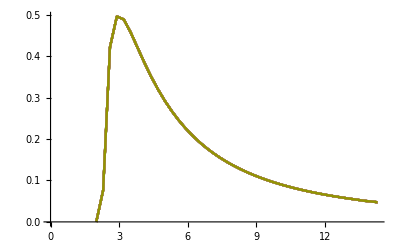

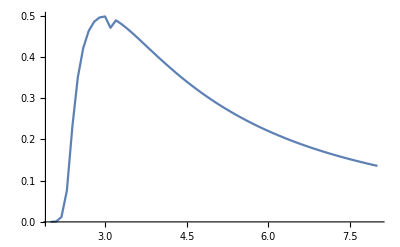

```mathematica
ListLinePlot[Second/@ptsNX]
```

```mathematica
ptsNNstar=Monitor[
Table[{m,σDiffNNtoNNstar[m]},{m,2.,8.,0.20}],
ProgressIndicator[m,{2.,8.}]
];
```

```mathematica
ptsNDstar=Monitor[
Table[{m,σDiffNNtoNDstar[m]},{m,2.,8.,0.20}],
ProgressIndicator[m,{2.,8.}]
];
```

```mathematica
ptsDNstar=Monitor[
Table[{m,σDiffNNtoDNstar[m]},{m,2.,6.,0.08}],
ProgressIndicator[m,{2., 8.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

```mathematica
ptsDDstar=Monitor[
Table[{m,σDiffNNtoDDstar[m]},{m,3.,7.,0.4}],
ProgressIndicator[m,{3.,7.}]
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ListLinePlot[{urqmdppTotal,urqmdppElastic, urqmdDiffND, urqmdDiffNNstar,urqmdDiffNDstar,urqmdDiffDD,urqmdDiffDNstar,urqmdDiffDDstar},PlotRange->All,PlotLegends->{"Total","Elastic","NΔ", "NN*", "NΔ*", "ΔΔ","ΔN*","ΔΔ*"}]
```

-Graphics-

```mathematica
ipTot[m_]:=Interpolation[urqmdppTotal,m,InterpolationOrder->1];
ipEl[m_]:=Interpolation[urqmdppElastic,m,InterpolationOrder->1];
ipStr[m_]:=Interpolation[urqmdppString,m,InterpolationOrder->1];
ipND[m_]:=Interpolation[urqmdDiffND,m,InterpolationOrder->1];
ipNNstar[m_]:=Interpolation[urqmdDiffNNstar,m,InterpolationOrder->1];
ipNDstar[m_]:=Interpolation[urqmdDiffNDstar,m,InterpolationOrder->1];
ipDD[m_]:=Interpolation[urqmdDiffDD,m,InterpolationOrder->1];
ipDNstar[m_]:=Interpolation[urqmdDiffDNstar,m,InterpolationOrder->1];
ipDDstar[m_]:=Interpolation[urqmdDiffDDstar,m,InterpolationOrder->1];
ipEx[m_]:=ipND@m+ipNNstar@m+ipNDstar@m+ipDD@m+ipDNstar@m+ipDDstar@m;
```

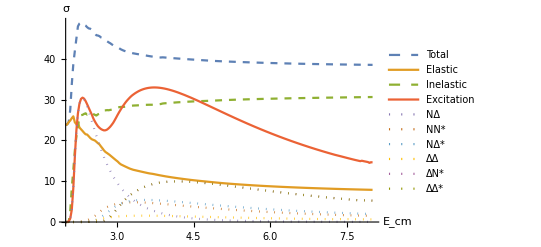

```mathematica
Plot[{ipTot[m],ipEl[m],ipTot[m]-ipEl[m],ipEx[m],
ipND[m],ipNNstar[m],ipNDstar[m],ipDD[m],ipDNstar[m],ipDDstar[m]},{m,2.,8.},PlotRange->All,PlotLegends->{"Total","Elastic","Inelastic","Excitation","NΔ", "NN*", "NΔ*", "ΔΔ","ΔN*","ΔΔ*"},
PlotStyle->{Dashed,Thick,Dashed,Thick,Dotted,Dotted,Dotted,Dotted,Dotted,Dotted},
AxesLabel->{"E_cm","σ"}
]
```

```mathematica
a[N1440,2.5]
```

0.144948

```mathematica
σDiffractiveNN[3.5,{N938,N1675}]
```

1.13302

```mathematica
Ds
```

{D1232,D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950}

```mathematica
pCMS[3.5, 0.938, 1.800] a[N1990,1.800]
```

0.931459

```mathematica
BR[N1675,{D1232,pi},1.8]
```

1.32463

```mathematica
m0@N1990
```

1.95

```mathematica
Γ0@N1990
```

0.55

```mathematica
Γ[N1675,{D1232,pi},1.8]/0.55
```

0.322035

```mathematica
a[N2190,1.8]
```

0.0552431

```mathematica
{N1440,N1520,N1535,N1650,N1675,N1680,N1700,N1710,N1720,N1900,N1990,N2080,N2190,N2220,N2250}
```

```mathematica
Table[a[h,2.5],{h,{D1232,D1600,D1620,D1700,D1900,D1905,D1910,D1920,D1930,D1950}}]//MatrixForm
```

(0.101957
0.195146
0.174841
0.18946
0.203345
0.246758
0.242799
0.222857
0.271666
0.262417)

```mathematica
ipDD[2.4]
```

0.00566667

```mathematica
ipEx[4.]
```

32.5132

```mathematica
p0Mean[1.7,{D1232,D1232},1]
```

0.

```mathematica
a[D1232,1.7]
```

0.328767

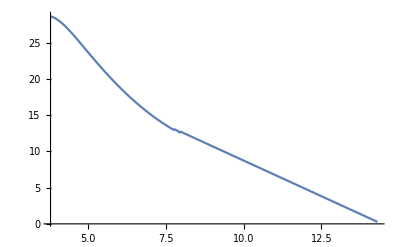

```mathematica
Plot[ipEx[m]*28.623/ipEx[3.8],{m,3.8,14.3},PlotRange->{0,All}]
```

```mathematica
Table[ipEx[m]*28.623/ipEx[3.8],{m,3.8,14.3,0.1}]
```

InterpolatingFunction::dmval: Input value {8.1} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{28.623,28.4801,28.2446,27.9334,27.566,27.1519,26.709,26.2366,25.7466,25.2436,24.7344,24.2218,23.7088,23.198,22.6918,22.1911,21.698,21.2129,20.7364,20.2698,19.8131,19.3665,18.9308,18.5055,18.0907,17.6866,17.293,16.9094,16.5365,16.1737,15.8204,15.4772,15.1432,14.8184,14.5037,14.1978,13.933,13.6465,13.3713,13.1129,13.0205,12.7895,12.677,12.4801,12.2832,12.0863,11.8894,11.6925,11.4956,11.2987,11.1018,10.9048,10.7079,10.511,10.3141,10.1172,9.92031,9.7234,9.52649,9.32958,9.13268,8.93577,8.73886,8.54195,8.34504,8.14814,7.95123,7.75432,7.55741,7.36051,7.1636,6.96669,6.76978,6.57287,6.37597,6.17906,5.98215,5.78524,5.58833,5.39143,5.19452,4.99761,4.8007,4.60379,4.40689,4.20998,4.01307,3.81616,3.61925,3.42235,3.22544,3.02853,2.83162,2.63471,2.43781,2.2409,2.04399,1.84708,1.65018,1.45327,1.25636,1.05945,0.862544,0.665636,0.468728,0.27182}

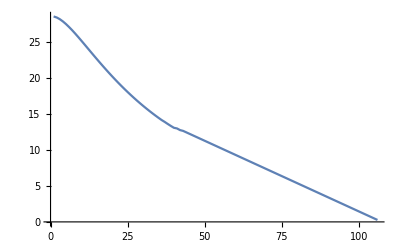

```mathematica
%//ListLinePlot
```

```mathematica
ipDiff[m_]:=ipND@m+ipNNstar@m+ipNDstar@m+ipDD@m+ipDNstar@m+ipDDstar@m;
```

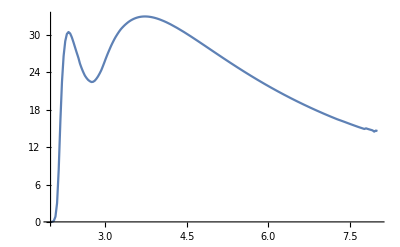

```mathematica
Plot[ipDiff[m],{m,2.,8.},PlotRange->All]
```

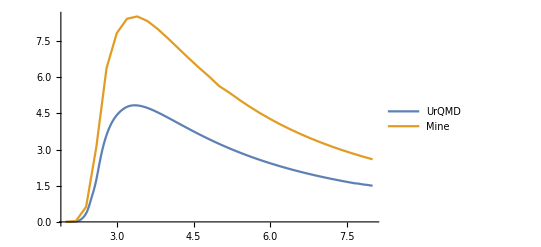

```mathematica
ListLinePlot[{urqmdppNNstar,ptsNNstar},PlotRange->All,PlotLegends->{"UrQMD","Mine"}]
```

```mathematica
Interpolation[ptsNNstar,2.5,InterpolationOrder->1]
```

1.86709

```mathematica
Interpolation[urqmdppNNstar,3,InterpolationOrder->1]
```

4.43107

```mathematica
minMass@D1232
```

1.077

```mathematica
a[D1232,2.]
```

0.189915

```mathematica
NIntegrate[a0[D1232,N@m],{m,-Infinity,Infinity}]
```

```mathematica
ipDD[2.5]
```

0.162667

```mathematica
aN[D1232]
```

Calculating aN for D1232

7.50257

```mathematica
a[D1232,2.]
```

Calculating aN for D1232

0.159048

```mathematica
minMass@D1232
```

1.077

```mathematica
pMean[2.3,{N938,D1232},1]
```

0.196174

```mathematica
Block[{hA=N938,hB=D1232,m0A=m0@N938,mDistribution=a,eCM=2.3,lFac=1,
mB=1.1},
pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB]
]
```

```mathematica
a0[D1232,1.1]
```

0.882904

```mathematica
pCMS[2.3,m0@N938,1.1]a0[D1232,1.1]
```

0.46946

```mathematica
pCMS[2.3,m0@N938,1.1]
```

0.531723

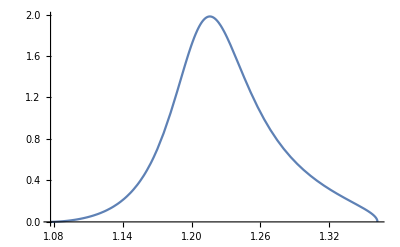

```mathematica
Block[{hA=N938,hB=D1232,m0A=m0@N938,mDistribution=a,eCM=2.3,lFac=1},
Plot[pCMS[eCM,m0A,mB]^lFac mDistribution[hB,mB],{mB,minMass@hB,eCM-m0@hA}]
]
```

```mathematica
σDiffractiveNN[2.3,{N938,D1232}]
```

30.0023

```mathematica
exciteSinglePts=Monitor[
Table[{eCM,Sum[σDiffractiveNN[eCM,{N938,h}],{h,excitations}]},{eCM,2.,4.,0.1}],
{ProgressIndicator[eCM,{2.,4.}],h}
]
```

First::normal: Nonatomic expression expected at position 1 in First[h].

Table::iterb: Iterator {products,decays[First[h]]} does not have appropriate bounds.

Total::normal: Nonatomic expression expected at position 1 in Total[products].

Table::iterb: Iterator {products,decays[First[h]]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

First::normal: Nonatomic expression expected at position 1 in First[h].

Total::normal: Nonatomic expression expected at position 1 in Total[products].

NIntegrate::inumr: The integrand a[h,mB] a[N938,mA] If[2.≤mA+mB,0,(√((2.^2-Power[«2»]) (2.^2-Power[«2»])))/(2. 2.)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

First::normal: Nonatomic expression expected at position 1 in First[h].

General::stop: Further output of First::normal will be suppressed during this calculation.

Total::normal: Nonatomic expression expected at position 1 in Total[products].

General::stop: Further output of Total::normal will be suppressed during this calculation.

NIntegrate::inumr: The integrand a[h,mB] a[N938,mA] If[2.≤mA+mB,0,(√((2.^2-Power[«2»]) (2.^2-Power[«2»])))/(2. 2.)] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

$Aborted

```mathematica
exciteDoublePts=Monitor[
Table[{eCM,Sum[σDiffractiveNN[eCM,{D1232,h}],{h,excitations}]},{eCM,2.,4.,0.1}],
{ProgressIndicator[eCM,{2.,4.}],h}
]
```

```mathematica
diffNNstarPts=Monitor[
Table[{eCM,σDiffNNtoNNstar[eCM]},{eCM,2.,4.,0.1}],
ProgressIndicator[eCM,{2.,8.}]
]
```

{{2.,0.},{2.1,0.0116068},{2.2,0.0908375},{2.3,0.507619},{2.4,1.63271},{2.5,4.26816},{2.6,7.16035},{2.7,10.5447},{2.8,11.6488},{2.9,12.059},{3.,12.1462},{3.1,12.1655},{3.2,12.0393},{3.3,11.7376},{3.4,11.3585},{3.5,10.9502},{3.6,10.5364},{3.7,10.1274},{3.8,9.73125},{3.9,9.34955},{4.,8.98332}}

```mathematica
diffNDPts=Monitor[
ClebschGordan[{1/2,1/2},{1/2,1/2},{1,1}]^2
*Table [{eCM,σDiffNNtoND[eCM]},{eCM,2.,8.,0.1}],
ProgressIndicator[eCM,{2.,8.}]
]
```

{{2.,0.},{2.1,4.1233},{2.2,45.8784},{2.3,47.3788},{2.4,39.1166},{2.5,31.1636},{2.6,24.6761},{2.7,19.5863},{2.8,15.6312},{2.9,12.5566},{3.,10.1559},{3.1,8.27022},{3.2,6.77905},{3.3,5.59181},{3.4,4.64015},{3.5,3.87219},{3.6,3.24896},{3.7,2.7398},{3.8,2.32155},{3.9,1.97611},{4.,1.68933},{4.1,1.45009},{4.2,1.24956},{4.3,1.08074},{4.4,0.938017},{4.5,0.816868},{4.6,0.713596},{4.7,0.625351},{4.8,0.549584},{4.9,0.484342},{5.,0.427967},{5.1,0.379148},{5.2,0.336708},{5.3,0.299723},{5.4,0.267403},{5.5,0.239087},{5.6,0.214216},{5.7,0.192318},{5.8,0.172994},{5.9,0.155899},{6.,0.140753},{6.1,0.127298},{6.2,0.115322},{6.3,0.104643},{6.4,0.0951023},{6.5,0.0865631},{6.6,0.0789068},{6.7,0.0720305},{6.8,0.0658445},{6.9,0.0602605},{7.,0.0552404},{7.1,0.0506941},{7.2,0.0465791},{7.3,0.0428492},{7.4,0.0394636},{7.5,0.0363866},{7.6,0.0335863},{7.7,0.0310344},{7.8,0.0287064},{7.9,0.02658},{8.,0.0246352}}

```mathematica
σDiffNNtoND[2.25]
```

49.6514

```mathematica
m0@N938+m0@D1232
```

2.17

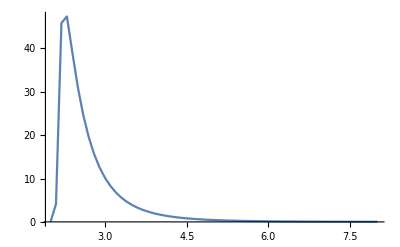

```mathematica
ListLinePlot[diffNDPts,PlotRange->All]
```

```mathematica
RuntimeTools`Profile[σDiffractiveNN[3.,{D1232,N1535}]]
```

2.00238

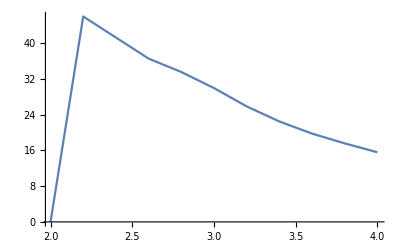

```mathematica
ListLinePlot[exciteSinglePts]
```

```mathematica
ptsSigmaLow=Monitor[
Table[{eCM,σDiffractiveNN[eCM]},{eCM,2.1,2.4,0.02}],
ProgressIndicator[eCM,{2.1,2.4}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{2.1,8.26437},{2.12,18.5243},{2.14,37.0006},{2.16,60.7773},{2.18,80.2787},{2.2,91.8804},{2.22,97.5281},{2.24,99.4959},{2.26,99.2625},{2.28,97.7135},{2.3,95.387},{2.32,92.6212},{2.34,89.6439},{2.36,86.6236},{2.38,83.7072},{2.4,81.033}}

```mathematica
σDiffractiveNN[2.36]
```

43.7892

```mathematica
43.98080047795236*GeVInv2mb
```

17.1252

```mathematica
ptsSigmaExcite=Monitor[
Table[{eCM,σDiffractiveNN[eCM]},{eCM,2.,8.,6./100}],
ProgressIndicator[eCM,{2.,8.}]
]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{2.,0.000617745},{2.06,1.0686},{2.12,18.5243},{2.18,80.2787},{2.24,99.4959},{2.3,95.387},{2.36,86.6236},{2.42,78.7182},{2.48,73.5645},{2.54,69.4046},{2.6,66.6729},{2.66,64.9214},{2.72,63.6901},{2.78,63.5323},{2.84,64.1132},{2.9,64.9813},{2.96,65.4032},{3.02,65.1517},{3.08,64.4909},{3.14,63.6252},{3.2,62.5723},{3.26,61.3723},{3.32,60.0287},{3.38,58.728},{3.44,57.3847},{3.5,55.9685},{3.56,54.6281},{3.62,53.3135},{3.68,52.0034},{3.74,50.738},{3.8,49.5067},{3.86,48.3137},{3.92,47.1492},{3.98,46.0334},{4.04,44.9427},{4.1,43.8854},{4.16,42.8643},{4.22,41.8329},{4.28,40.9102},{4.34,39.9877},{4.4,39.0329},{4.46,38.218},{4.52,37.3718},{4.58,36.5558},{4.64,35.7604},{4.7,34.9989},{4.76,34.2472},{4.82,33.5235},{4.88,32.7897},{4.94,32.1415},{5.,31.4802},{5.06,30.8387},{5.12,30.2176},{5.18,29.6125},{5.24,28.9382},{5.3,28.4537},{5.36,27.8959},{5.42,27.3588},{5.48,26.7756},{5.54,26.3229},{5.6,25.7945},{5.66,25.3475},{5.72,24.63},{5.78,24.4199},{5.84,23.9735},{5.9,23.5383},{5.96,23.1219},{6.02,22.7083},{6.08,22.3076},{6.14,21.9169},{6.2,21.5358},{6.26,21.1392},{6.32,20.8023},{6.38,20.4532},{6.44,20.1657},{6.5,19.7674},{6.56,19.4421},{6.62,19.1261},{6.68,18.8113},{6.74,18.508},{6.8,18.2074},{6.86,18.0433},{6.92,17.6342},{6.98,17.3579},{7.04,17.0862},{7.1,16.778},{7.16,16.5633},{7.22,16.3119},{7.28,16.0619},{7.34,15.8222},{7.4,15.5676},{7.46,15.3546},{7.52,15.111},{7.58,14.9025},{7.64,14.6892},{7.7,14.4771},{7.76,14.2649},{7.82,14.0618},{7.88,13.8678},{7.94,13.6707},{8.,13.4802}}

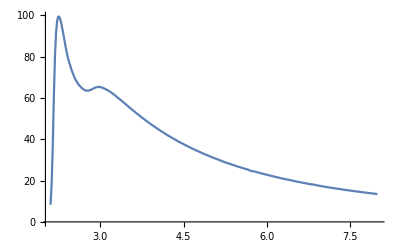

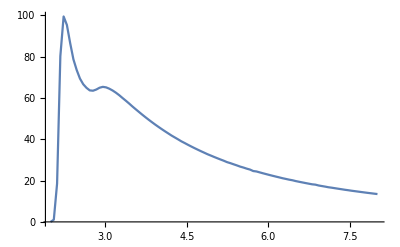

```mathematica
ListLinePlot[ptsSigmaLow~Join~(ptsSigmaExcite[[8;;101]])]
```

```mathematica
evenSpacedPts=Table[{x,Interpolation[ptsSigmaExcite[[1;;2]]~Join~ptsSigmaLow~Join~ptsSigmaExcite[[8;;101]],x]},{x,2.,8.,6./300}];
```

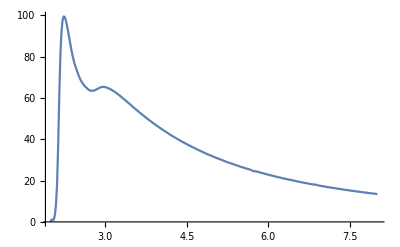

```mathematica
ListLinePlot@evenSpacedPts
```

```mathematica
Second/@evenSpacedPts
```

{0.000617745,1.15627,0.988159,1.0686,3.38951,8.26437,18.5243,37.0006,60.7773,80.2787,91.8804,97.5281,99.4959,99.2625,97.7135,95.387,92.6212,89.6439,86.6236,83.7072,81.033,78.7182,76.7261,75.0204,73.5645,72.046,70.654,69.4046,68.3575,67.4525,66.6729,66.0029,65.4247,64.9214,64.4258,64.0086,63.6901,63.5348,63.4863,63.5323,63.6661,63.8653,64.1132,64.4069,64.7053,64.9813,65.1827,65.3262,65.4032,65.3811,65.294,65.1517,64.9668,64.744,64.4909,64.2242,63.9355,63.6252,63.2931,62.9416,62.5723,62.1885,61.7884,61.3723,60.9312,60.481,60.0287,59.5946,59.1621,58.728,58.2865,57.8391,57.3847,56.9134,56.4395,55.9685,55.5158,55.0696,54.6281,54.1881,53.7502,53.3135,52.8743,52.4371,52.0034,51.5771,51.1554,50.738,50.3235,49.9131,49.5067,49.1052,48.7077,48.3137,47.9213,47.5329,47.1492,46.773,46.4014,46.0334,45.6666,45.303,44.9427,44.5864,44.2339,43.8854,43.5433,43.2035,42.8643,42.5158,42.1705,41.8329,41.5187,41.2124,40.9102,40.6043,40.2972,39.9877,39.6645,39.3441,39.0329,38.7541,38.4846,38.218,37.9363,37.6535,37.3718,37.0969,36.825,36.5558,36.2877,36.0224,35.7604,35.504,35.2505,34.9989,34.7464,34.4956,34.2472,34.0047,33.764,33.5235,33.2753,33.0295,32.7897,32.569,32.3541,32.1415,31.9209,31.7,31.4802,31.2641,31.0503,30.8387,30.6296,30.4226,30.2176,30.0183,29.8177,29.6125,29.3826,29.1547,28.9382,28.7686,28.6104,28.4537,28.2713,28.0842,27.8959,27.7179,27.5397,27.3588,27.1608,26.9642,26.7756,26.6204,26.472,26.3229,26.1474,25.9694,25.7945,25.6538,25.5091,25.3475,25.0999,24.8512,24.63,24.5403,24.4794,24.4199,24.2851,24.1333,23.9735,23.8268,23.6816,23.5383,23.3982,23.2596,23.1219,22.9832,22.8452,22.7083,22.5734,22.4399,22.3076,22.1763,22.0461,21.9169,21.7901,21.6634,21.5358,21.4017,21.2685,21.1392,21.0238,20.9124,20.8023,20.6836,20.5664,20.4532,20.3591,20.2654,20.1657,20.0362,19.9011,19.7674,19.654,19.5464,19.4421,19.3361,19.2309,19.1261,19.0205,18.9154,18.8113,18.7094,18.6084,18.508,18.4009,18.2991,18.2074,18.1564,18.1064,18.0433,17.9155,17.7744,17.6342,17.5336,17.4431,17.3579,17.2688,17.1788,17.0862,16.9811,16.8768,16.778,16.7024,16.6325,16.5633,16.4817,16.3974,16.3119,16.228,16.1445,16.0619,15.9821,15.9025,15.8222,15.7362,15.6506,15.5676,15.4955,15.4254,15.3546,15.2736,15.1915,15.111,15.0396,14.9706,14.9025,14.8317,14.7605,14.6892,14.6185,14.5478,14.4771,14.4059,14.3351,14.2649,14.1962,14.1285,14.0618,13.9967,13.9322,13.8678,13.802,13.7362,13.6707,13.606,13.5424,13.4802}

```mathematica
Plot[σDiffractiveNN[eCM,{N938,D1600}],{eCM,2.,6.},PlotRange->All]
```

$Aborted

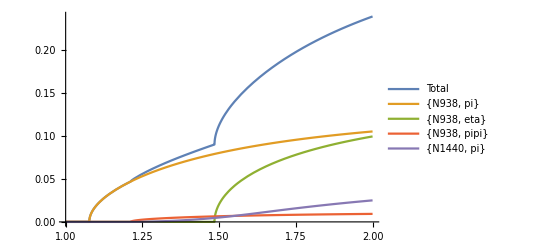

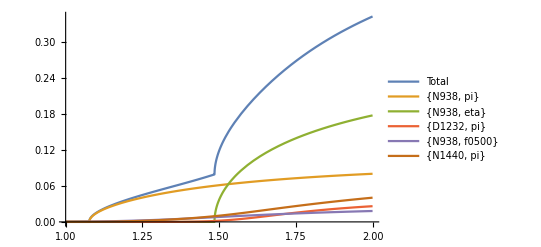

```mathematica
Block[{h=N1535},
Plot[Evaluate@Flatten@{Γ[h,m],Table[Γ[h,hs,m],{hs,decayProducts@h}]},{m,1.,2.},PlotLegends->Flatten@{"Total",ToString/@decayProducts[h]},
PlotRange->All
]
]
```

```mathematica
pMean[3.0,{N938,D1232}]
```

0.796906

```mathematica
massDecayBound@D1232
```

1.077

```mathematica
Γ0@N938
```

0.

```mathematica
Γ0@D1232
```

0.115

```mathematica
2m0@D1232
```

2.464

```mathematica
pMean[2.5,{D1232,D1232}]
```

{1.077,2.5}{1.077,1.423}

0.188874

```mathematica
m0@N938+m0@D1232
```

2.17

```mathematica
pMean[2.5,{N938,D1232}]
```

0.679627

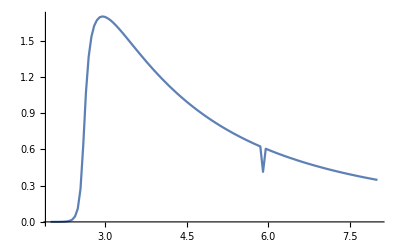

```mathematica
pts= Monitor[
Table[{eCM,sigmapp[eCM,{N938,D1600}]},{eCM,2.0,8.0,0.05}],
ProgressIndicator[eCM,{2.,8.}]
];
ListLinePlot[pts,PlotRange->All]
```

```mathematica
σNNlow=1.8964808;σNNhigh=2.8964808;
σppTable=Transpose[{Table[1.8964808+0.01(n-1),{n,1,100}],{ 39.48,31.76,26.26,24.05,23.94,23.77,23.72,23.98,24.48,24.52,28.72,33.21,37.33,39.87,42.14,44.15,46.85,48.56,48.65,48.97,48.81,48.43,48.36,48.19,47.89,47.53,47.42,47.37,47.17,46.65,46.48,45.94,45.63,45.75,45.52,45.24,45.13,44.96,44.55,44.44,44.10,43.89,43.77,43.32,43.30,43.07,42.95,42.74,42.46,42.28,42.11,41.96,41.86,41.74,41.64,41.54,41.44,41.37,41.29,41.22,41.14,41.09,41.01,40.93,40.83,40.74,40.66,40.58,40.51,40.47,40.40,40.35,40.47,40.44,40.38,40.35,40.32,40.27,40.25,40.23,40.19,40.13,40.11,40.09,40.06,40.02,40.00,39.95,39.94,39.90,39.87,39.82,39.77,39.72,39.67,39.59,39.54,39.48,39.41,39.32}
}];
σpnTable=Transpose[{Table[1.8964808+0.01(n-1),{n,1,100}],
{ 248.20,93.38,55.26,44.50,41.33,38.48,37.20,35.98,35.02,34.47,34.37,34.67,35.23,35.97,36.75,37.37,37.77,38.03,38.40,38.83,39.26,39.67,40.06,40.45,40.79,41.06,41.31,41.52,41.70,41.81,41.87,41.98,42.12,42.29,42.55,42.82,43.01,43.12,43.16,43.14,43.06,42.95,42.81,42.67,42.54,42.45,42.38,42.33,42.30,42.29,42.28,42.26,42.24,42.21,42.17,42.14,42.10,42.07,42.06,42.05,42.04,42.03,42.02,42.00,41.97,41.94,41.89,41.84,41.79,41.73,41.67,41.61,41.55,41.49,41.44,41.38,41.34,41.31,41.29,41.28,41.27,41.28,41.30,41.33,41.36,41.40,41.44,41.49,41.50,41.51,41.51,41.51,41.52,41.51,41.51,41.50,41.50,41.49,41.47,41.46}
}];
```

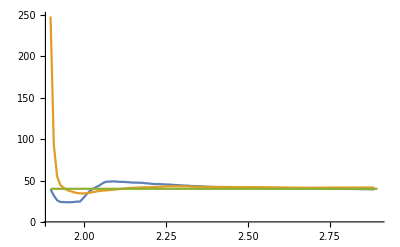

```mathematica
ListLinePlot[{σppTable,σpnTable,Table[{x,40},{x,σNNlow,σNNhigh}]},PlotRange->{0,All}]
```

```mathematica
Length@σppTable
```

100

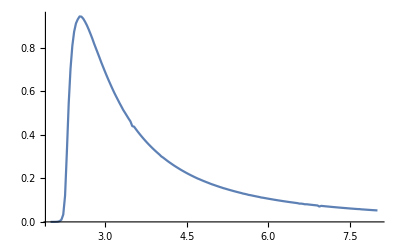

```mathematica
ListLinePlot@brFactorPts[{D1232,D1620}]
```

```mathematica
Length@brFactorPts[{D1232,D1620}]
```

181

```mathematica
(x=4)≠4
```

False